# Fully Interpolated Field : |V| & ϵ̇

```mathematica
(* *)
```

```mathematica
images=Import["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@optic flow\\C10 - cropped.tif"][[;;160]];
midimage=Ceiling[1/2Length[images]];
image=images[[midimage]];
midmask=Import["C:\\Users\\aliha\\Desktop\\research related\\raw data\\@optic flow\\mid-mask.tif"];
```

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\optic flow\\final iterpolated field\\BoundaryregTrans_meanF.mx";
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\optic flow\\final iterpolated field\\BoundaryregTrans_meanU.mx";
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\optic flow\\final iterpolated field\\BoundaryregTrans_meanV.mx";
```

```mathematica
(*<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\optic flow\\final iterpolated field\\ImgregTrans_meanF.mx";
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\optic flow\\final iterpolated field\\ImgregTrans_meanU.mx";
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\optic flow\\final iterpolated field\\ImgregTrans_meanV.mx";*)
```

```mathematica
interpU =Interpolation[meanflowfU,InterpolationOrder->1]
interpV =Interpolation[meanflowfV,InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

```mathematica
x1=26;x2=219;y1=33;y2=220;
```

```mathematica
interpfield=With[{reg=ConvexHullMesh[flowfF[[All,1]]]},
ContourPlot[Norm[{interpU[x,y],interpV[x,y]}],{x,x1,x2},{y,y1,y2},
WorkingPrecision->20,PlotPoints->25,Frame-> False,
ColorFunction->"Rainbow",Contours->50,MeshFunctions->{#1&,#2&},ContourStyle->None,PerformanceGoal->"Quality",
RegionFunction->Function[{x,y,z},RegionMember[reg,{x,y}]],AspectRatio->1
]
];
```

```mathematica
Rasterize[
ImageRotate[Show[ImageRotate[HighlightImage[
SetAlphaChannel[ImageAdjust@image,
ImageAdd[Image[GaussianFilter[midmask,10],"Real"],0]],{"Boundary",Black,midmask}],Pi/2],
interpfield,Axes-> {False,False},Frame-> True,FrameTicks-> False],-Pi/2],"Image",RasterSize->512]
```

-Graphics-

```mathematica
ListDiv[σ_]:=flow↦GaussianFilter[flow[[All,All,1]],σ{2,1},{0,1},Padding->"Fixed"]-
GaussianFilter[flow[[All,All,2]],σ{2,1},{1,0},Padding->"Fixed"]
```

```mathematica
inter=Quiet@With[{reg=RegionMember@ConvexHullMesh[flowfF[[All,1]]]},
Table[If[reg[{x,y}],{interpU[x,y],interpV[x,y]},{0.,0.}],{x,x1,x2},{y,y1,y2}]
];
```

```mathematica
div=ListDiv[18][inter];
```

```mathematica
ImageMultiply[ImagePad[ColorCombine[{ConstantImage[0,{188,194}],Image[500div],Image[500div]},"LAB"],{{5,4},{5,5}}],ImageRotate[ImageCrop@midmask,90Degree]]//ImageRotate[#,-90Degree]&
```

-Graphics-

```mathematica
fullInterpField=With[{reg=ConvexHullMesh@flowfF[[All,1]]},
DeleteCases[#,Null]&@Flatten[Table[If[RegionMember[reg,{x,y}],{{x,y},{Quiet@interpU[x,y],Quiet@interpV[x,y]}},Sequence[]],{x,x1,x2},{y,y1,y2}],1]
];
```

## Velocity Gradient ∇ | Strain Rate

```mathematica
SetAttributes[makeVecs,HoldAll];
makeVecs[vals_,vecs_,s_,rQ_]:=With[{n=Length[vals]},If[TrueQ[rQ],Do[Switch[Sign[Im[vals[[k]]]],0,Null,1,vecs[[k]]+=s I vecs[[k+1]],-1,vecs[[k]]=Conjugate[vecs[[k-1]]]],{k,n}]]]

Options[getEigensystem]={Mode->Automatic};

getEigensystem[mat_?SquareMatrixQ,opts:OptionsPattern[]]:=Module[{m=mat,chk,ei,ev,lm,lv,n,rm,rQ,rv},

n=Length[mat];
Switch[OptionValue[Mode],
Right|Automatic,
{lm,rm}={"N","V"},
Left,{lm,rm}={"V","N"},
All,{lm,rm}={"V","V"},
_,{lm,rm}={"N","V"}];
LinearAlgebra`LAPACK`GEEV[lm,rm,m,ev,ei,lv,rv,chk,rQ];
If[!TrueQ[chk],
Message[getEigensystem::eivec0];
Return[$Failed,Module]
];
If[rQ,ev+=I ei];
Switch[OptionValue[Mode],Right|Automatic,rv=ConjugateTranspose[rv];
makeVecs[ev,rv,1,rQ];{ev,rv},Left,lv=ConjugateTranspose[lv];
makeVecs[ev,lv,-1,rQ];{ev,lv},All,{lv,rv}=ConjugateTranspose/@{lv,rv};
makeVecs[ev,rv,1,rQ];makeVecs[ev,lv,-1,rQ];
{ev,rv,lv},_,rv=ConjugateTranspose[rv];
makeVecs[ev,rv,1,rQ];{ev,rv}]
];
```

```mathematica
Clear@meshgrid;
meshgrid[int1_Integer,int2_Integer]:=Transpose[
{ConstantArray[Range[int1],int2],Transpose@ConstantArray[Range[int2],int1]},
{3,2,1}];
meshgrid[list1_List,list2_List]:=Transpose[
{ConstantArray[list1,Length@list2], Transpose@ConstantArray[list2,Length@list1]},
{3,2,1}];
```

```mathematica
Unprotect[None,Power];
None/:Subtract[None,None]:=None;
None/:Subtract[None,_Real|_Integer]:=None;
None/:Subtract[_Real|_Integer,None]:=None;
None/:Plus[None,-None]:=None;
None/:Plus[None,_Real|_Integer]:=None;
None/:Times[Rational[_,_],None]:=None;
None/:Times[_Integer|_Real,None]:=None;
None/:Times[None,None]:=None;
Power/:Times[_,Power[None,_]]:=None;
Protect[None,Power];
```

```mathematica
Unevaluated[x]/:grad[Unevaluated[x],array_,div_]:=Block[{arr,nx,ny,diffL,diffR,diff},
{nx,ny}={#[[1]],#[[2]]}&[Dimensions[array]];
arr=PadLeft[PadRight[array,{nx,ny+1},None],{nx,ny+2},None];
diffL=arr[[All,2;;ny+1]]-arr[[All,1;;ny]];
diffR=arr[[All,3;;ny+2]]-arr[[All,2;;ny+1]];
diff=(diffL+diffR)/2;
diff/div
];

Unevaluated[y]/:grad[Unevaluated[y],array_,div_]:=Block[{arr,nx,ny,diffL,diffR,diff},
{nx,ny}={#[[1]],#[[2]]}&[Dimensions[array]];
arr=PadLeft[PadRight[array,{nx+1,ny},None],{nx+2,ny},None];
diffL=arr[[2;;nx+1,All]]-arr[[1;;nx,All]];
diffR=arr[[3;;nx+2,All]]-arr[[2;;nx+1,All]];
diff=(diffL+diffR)/2;
diff/div
];
```

```mathematica
pts=Round@fullInterpField[[All,1]];
{ymin,ymax}=MinMax@pts[[All,1]];
{xmin,xmax}=MinMax@pts[[All,2]];
array=meshgrid[Range[ymin,ymax],Range[xmin,xmax]];
```

```mathematica
allpts=Flatten[array,1];
ptsinDomain=Pick[allpts,RegionMember[ConvexHullMesh@pts][allpts],True];
flowinDomain=Thread[{ptsinDomain,Transpose[Quiet@Apply[#,ptsinDomain,{1}]&/@{interpU,interpV}]}];
```

```mathematica
dgrad=dgrid=7;
{pts,vel}=flowinDomainᵀ;
{ymin,ymax}=MinMax@pts[[All,1]];
{xmin,xmax}=MinMax@pts[[All,2]];
array=meshgrid[Range[ymin,ymax,dgrid],Range[xmin,xmax,dgrid]];
gridpts=Flatten[array,1]∩flowinDomain[[All,1]];
{ny,nx}={#[[1]],#[[2]]}&[Dimensions[array]];
```

```mathematica
grid=Replace[Replace[array,Dispatch[Thread[pts->vel]],{2}],{__Integer} -> {None,None},{2}];
```

```mathematica
(*ux,vx,uy,vy*)
ux=grad[Unevaluated[x],grid[[All,All,2]],dgrad];
vx=grad[Unevaluated[x],grid[[All,All,1]],dgrad];
uy=grad[Unevaluated[y],grid[[All,All,2]],dgrad];
vy=grad[Unevaluated[y],grid[[All,All,1]],dgrad];
```

```mathematica
DVxx = (ux);
DVyx=DVxy =(uy+vx)/2;
DVyy=(vy);
DVww=(-uy+vx); (*rotation*)
trace=(DVxx+DVyy)/2;
```

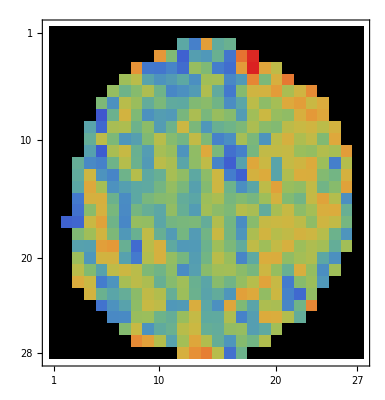
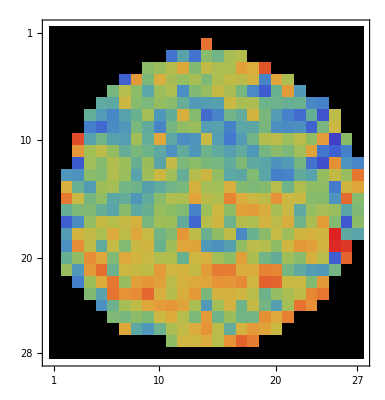
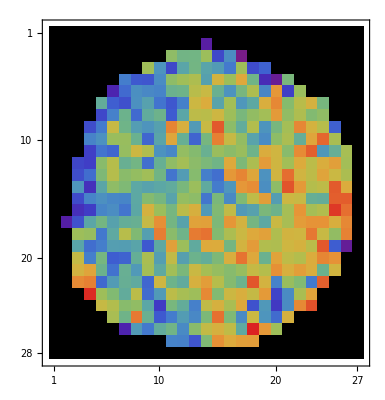
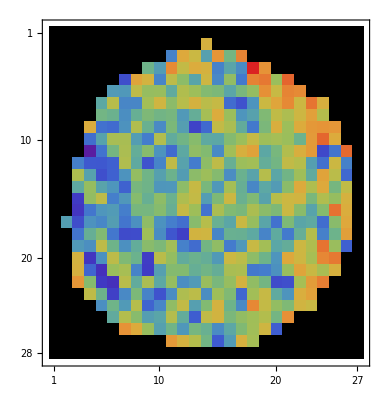
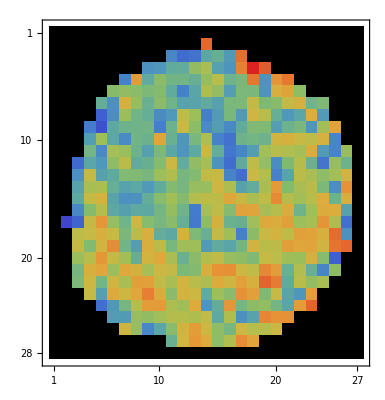
{xx→-Graphics-,yy→-Graphics-,yx→-Graphics-,xy→-Graphics-,ww→-Graphics-,trace→-Graphics-}

```mathematica
Thread[{"xx","yy","yx","xy","ww","trace"}->(MatrixPlot[#,ColorFunction->"Rainbow",ColorRules->{0->Black}]&/@({DVxx,DVyy,DVyx,DVxy,DVww,trace}/.None-> 0))]
```

```mathematica
ColorData["CandyColors"]
```

ColorDataFunction[…]

```mathematica
pos=SparseArray[(DVxx*DVyy*DVxy)/.None->0]["NonzeroPositions"];
```

```mathematica
Clear@plotbars;
With[{imgdim2=Last@ImageDimensions[image]},
plotbars[ϕ_,eigval_,scale_,inds_]:=Module[{Amp,x0,y0,xmaj,ymaj},
Amp=scale Abs[eigval];
{y0,x0}=array[[Sequence@@inds]];
{xmaj,ymaj}=Amp Through[{Cos,Sin}[ϕ]];
Line[Abs[{0,imgdim2}-{##}]&@@@Thread[{xmaj {-1,1}+x0,ymaj {-1,1}+y0}]]
]
];
```

```mathematica
midimage=Ceiling[3/4 Length[images]];
ptsTransfer=With[{imgdim=Last@ImageDimensions[images[[midimage]]]},
{#[[2]],imgdim-#[[1]]}&/@gridpts
];
```

```mathematica
HighlightImage[images[[midimage]],{Opacity[0.5],gridpts,Blue,ptsTransfer}]
```

-Graphics-

```mathematica
{err,transFnPts}=FindGeometricTransform[ptsTransfer,gridpts]
```

{3.85134×10^-14,TransformationFunction[(2.77556×10^-16 | 1. | -1.13687×10^-13
-1. | -2.22045×10^-16 | 244.
0. | 0. | 1.)]}

```mathematica
{pt,dir}=Mean/@{N@fullInterpField[[All,1]],fullInterpField[[All,2]]};
θ=(ArcTan[#[[2]]/#[[1]]]&[dir]);
graphicsPrimitive={};
Do[
DV={{(DVxx[[Sequence@@i]]-DVyy[[Sequence@@i]])/2,DVxy[[Sequence@@i]]},
{DVxy[[Sequence@@i]],-(DVxx[[Sequence@@i]]-DVyy[[Sequence@@i]])/2 }}; 

If[FreeQ[DV,None],
(*{eVa,eVe}={DiagonalMatrix[#[[1]]],#[[2]]}&@Eigensystem[DV];*)
{eVa,eVe}={DiagonalMatrix[Reverse@#[[1]]],Reverse[-#[[2]]]}&[Re@getEigensystem[DV]];
vp1=Diagonal[eVa];
{val1,ind1}={Sort@vp1,Ordering@vp1};
ϕ= ArcTan[eVe[[2,ind1[[2]] ]]/eVe[[1,ind1[[2]] ]] ];
rvect={eVe[[1,ind1[[2]] ]],eVe[[2,ind1[[2]] ]]};

rotationTrans=RotationTransform[θ];
rvectTurned=rotationTrans[rvect];
scalar=Abs[First@rvectTurned];

{minDv,maxDv} = MinMax[eVa];
Tracee = (DVxx[[Sequence@@i]]+DVyy[[Sequence@@i]])/2;

Block[{prim},
If[Abs[minDv]*Abs[maxDv]>0,
prim=GeometricTransformation[
Circle[transFnPts@array[[Sequence@@i]],{Round[500Abs[Tracee]],Round[Abs[500 Tracee]]}],
RotationTransform[ϕ,transFnPts@array[[Sequence@@i]]]
];
If[Tracee>0,
(*isotropic strain-rate*)
AppendTo[graphicsPrimitive,{prim}~Prepend~Red],
AppendTo[graphicsPrimitive,{prim}~Prepend~Blue]
];
(*anisotropic strain-rate*)
AppendTo[graphicsPrimitive,
{ColorData["CandyColors"][scalar],Thickness[0.005],plotbars[ϕ,maxDv,500,i]}]
]
]
],{i,pos}]
```

```mathematica
ptsVelAssoc=AssociationThread[flowinDomain[[All,1]],flowinDomain[[All,-1]]];
transVec=TransformationFunction[ReplacePart[Chop@transFnPts[[1]],{2,3}->0]];
meanflowRot=Thread[{ptsTransfer,transVec[#]&/@Lookup[ptsVelAssoc,gridpts]}];
{pt,dir}=Mean/@{N@meanflowRot[[All,1]],meanflowRot[[All,2]]};
```

```mathematica
midimage=Ceiling[1/2 Length[images]];
Image[
Rasterize[Show[
HighlightImage[
SetAlphaChannel[ImageAdjust@images[[midimage]],
ImageAdd[Image[GaussianFilter[midmask,5],"Real"],0.]],{"Boundary",Black,midmask}],
Graphics[If[!FreeQ[#,0,Infinity],{Opacity[0.5],Thickness[0.004],#},{Thin,#}]&/@graphicsPrimitive],
Graphics[{Thick,GrayLevel[0],Arrowheads[{{.035,1,{-Graphics-,1}}}],Arrow[{pt,(pt+200dir)}]}],
ImageSize->Large],"Image",ImageResolution->500],
ImageSize->Medium]
```

-Graphics-

```mathematica
<<"C:\\Users\\aliha\\Desktop\\analysis notebooks\\optic flow\\@KLT scripts\\VectorFieldOperations.m";
```

```mathematica
{graphicsPrimitive,meanflowRot}=SRMeasures[images[[midimage]],flowfF,DVxx,DVyy,DVxy,array];
```

```mathematica
Graphics[{graphicsPrimitive,Thick,Line@ImageMeasurements[midmask,"PerimeterPositions"]},
Frame->True,FrameTicks->None,Axes->{False,False},ImageSize->Medium]
```

-Graphics-

```mathematica
DownValues[SRMeasures]=Replace[DownValues[SRMeasures],XYZColor[y__,p_]:> XYZColor[y,0.75],{0,Infinity}];
```

```mathematica
{graphicsPrimitive,meanflowRot}=SRMeasures[images[[midimage]],fullInterpField,DVxx,DVyy,DVxy,array];
```

```mathematica
Rasterize[Graphics[{graphicsPrimitive,Thick,Line@ImageMeasurements[midmask,"PerimeterPositions"]},
Frame->True,FrameTicks->None,Axes->{False,False},ImageSize->Medium],"Graphics",RasterSize->1024]
```

-Graphics-